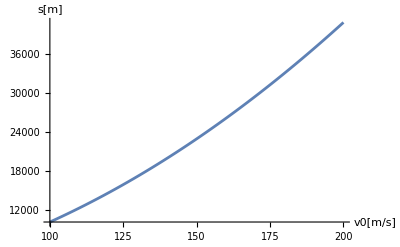

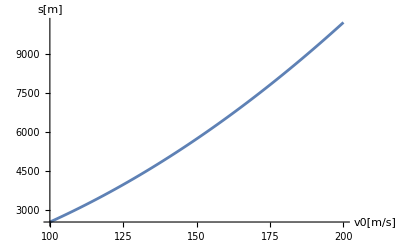

```mathematica
ClearAll["Global`*"]
mc := 1000;
m1 = mc - m2;
m2 = mc* x;
alpha := 45;
v0r = v0 * Cos[alpha Degree];

ppocz = mc * v0r;
p1 = m1*v1;
p2 =m2*v2;
v1 =v0r;



roz1 = Solve[ppocz == p2-p1,v2];
v2 /.roz1[[1]];
g = 9.81;
zuk =(v0 ^2 * Sin[2 * alpha Degree])/g;
huk =  (v0 ^2 * Sin[alpha Degree]^2)/(2*g);
zpoz = v2 * Sqrt[(2*huk)/g]/.roz1 ;
zasieg = 1/2 * zuk+zpoz;

rys1 = Plot[zasieg /.x->0.1  , {v0, 100, 200}, AxesLabel->{HoldForm["v0[m/s]"],HoldForm["s[m]"]}]
rys2 = Plot[zasieg /.x->0.4  , {v0, 100, 200}, AxesLabel->{HoldForm["v0[m/s]"],HoldForm["s[m]"]}]
```